## NEW reading in excel stuff

This code takes a bunch of excel sheets and data from long time-course assays and condenses it into .dat files with exactly the same format. This way, I can write a code to easily view and graph the data
I’m cleaning up stable and transient assays, TA, TL and NT.

## Read in .dat files

```mathematica
(*myFolder = "C:\\Users\\Charlotte\\Dropbox (Personal)\\_copy_old lab NB notes\\"
```

```mathematica
myFolder = "/Users/ccialek/Dropbox (Personal)/_copy_old lab NB notes"
```

/Users/ccialek/Dropbox (Personal)/_copy_old lab NB notes

```mathematica
myNT2=<<(myFolder<>"/102017_Imaging_14-5h_results_NT.dat");
myTA2=<<(myFolder<>"/102017_Imaging_14-5h_results_TA.dat");
myTL2=<<(myFolder<>"/102017_Imaging_14-5h_results_TL.dat");
myTA1=<<(myFolder<>"/1004-517_Imaging_14-5h_results2_TA.dat");
myNT1=<<(myFolder<>"/1004-517_Imaging_14-5h_results2_NT.dat");
myTA3=<<(myFolder<>"/120317_Imaging_14-5h_results_TA_loRNA_cells.dat");
myNT3=<<(myFolder<>"/120317_Imaging_14-5h_results_NT_loRNA_cells.dat");
myTL3=<<(myFolder<>"/120317_Imaging_14-5h_results_TL_loRNA_cells.dat");
```

```mathematica
myNT -> 18, 13,25
myTA -> 13, 18, 26
myTL ->  , 13, 18
```

```mathematica
myTL2//Dimensions
myTL3//Dimensions
```

{13,7,1}

{18,2,1}

## Graphs: Accumulation: Removing cells with HIGH early accumulation

```mathematica
NTdata = Join[myNT1, myNT2];
TAdata = Join[myTA1, myTA2];
TLdata = Join[myTL2];
```

```mathematica
rmNTdata = NTdata//Cases[#,x_/; x⟦4,1,2,2⟧≤ .2]&;
rmTLdata = TLdata//Cases[#,x_/; x⟦4,1,2,2⟧≤ .2]&;
rmTAdata = TAdata//Cases[#,x_/; x⟦4,1,2,2⟧≤ .2]&;
```

```mathematica
NTdata[[5,2,1,2,2]]
```

44.

```mathematica
NTdata[[All,2,1,o,2]]
```

Part::pkspec1: The expression o cannot be used as a part specification.

```mathematica
Row[{"TA  ","included   " ,"    dataset1 " ,Length@rmTA1[[1]] ,"    dataset2 " ,Length@rmTA2[[1]] ,"    dataset3 " ,Length@rmTA3[[1]]}]
Row[{"NT  ","included   " ,"    dataset1 ",Length@rmNT1[[1]] ,"    dataset2 " ,Length@rmNT2[[1]] ,"    dataset3 " ,Length@rmNT3[[1]]}]
Row[{"TL  ","included   " ,"    dataset1 ",0  ,"     dataset2 " ,Length@rmTL2[[1]] ,"    dataset3 " ,Length@rmTL3[[1]]}]
```

TA  included       dataset1 11    dataset2 16    dataset3 20

NT  included       dataset1 18    dataset2 16    dataset3 14

TL  included       dataset1 0     dataset2 12    dataset3 13

### Graphs...

#### Cy3 accumulation :

Make lists of {time,accumulation} for each of the 2 or 3 datasets, removing any cells with >20% accumulation at the first time point!

```mathematica
rmNT1 = myNT1//Cases[#,x_/; x⟦4,1,2,2⟧≤ .2]&//#⟦All,4⟧&;
rmTA1 = myTA1//Cases[#,x_/; x⟦4,1,2,2⟧≤ .2]&//#⟦All,4⟧&;
rmNT2 = myNT2//Cases[#,x_/; x⟦4,1,2,2⟧≤ .2]&//#⟦All,4⟧&;
rmTL2 = myTL2//Cases[#,x_/; x⟦4,1,2,2⟧≤ .2]&//#⟦All,4⟧&;
rmTA2 = myTA2//Cases[#,x_/; x⟦4,1,2,2⟧≤ .2]&//#⟦All,4⟧&;
rmNT3 = myNT3//Cases[#,x_/; x⟦2,1,2,2⟧≤ .2]&//#⟦All,2⟧&;
rmTL3 = myTL3//Cases[#,x_/; x⟦2,1,2,2⟧≤ .2]&//#⟦All,2⟧&;
rmTA3 = myTA3//Cases[#,x_/; x⟦2,1,2,2⟧≤ .2]&//#⟦All,2⟧&;
```

Make SUPER list of {time,accumulation} per each treatment

```mathematica
myNTaccum = Join[rmNTdata⟦All,4,1,All⟧,Flatten[rmNT3⟦All⟧,1]];
Dimensions[myNTaccum]
```

{43}

```mathematica
myTAaccum = Join[rmTAdata⟦All,4,1,All⟧,Flatten[rmTA3⟦All⟧,1]];
Dimensions[myTAaccum]
```

{46}

```mathematica
myTLaccum = Join[rmTLdata⟦All,4,1,All⟧,Flatten[rmTL3⟦All⟧,1]];
Dimensions[myTLaccum]
```

{25,6,2}

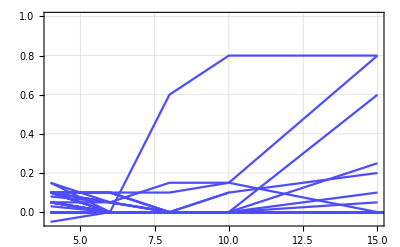
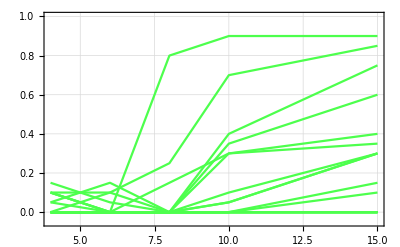
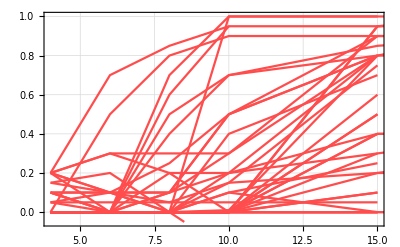

```mathematica
paccumTL=myTLaccum[[All,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.3],Joined->True,PlotTheme->"Detailed",ImageSize->400, PlotRange -> {{4,15},{-.05, 1}}]&;
paccumNT=myNTaccum[[All,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.3],Joined->True,PlotTheme->"Detailed",PlotRange -> {{4,15},{-.05, 1}},ImageSize->400]&;
paccumTA=myTAaccum[[All,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.3],Joined->True,PlotTheme->"Detailed",PlotRange -> {{4,15},{-.05, 1}},ImageSize->400]&;
Row[{
paccumTA, paccumTL, paccumNT
}]
```

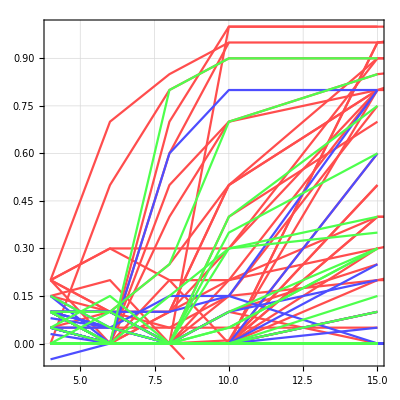

```mathematica
Show[paccumNT,paccumTA,paccumTL,AspectRatio->1, PlotRange -> {{4,15},{-.05, 1}}]
```

#### Now, only plot the averages

-> take the average of ALL data
-> find the SEM error of the data sets

```mathematica
mytimes = myTAaccum[[1,2;;6,1]];
TAaccum = myTAaccum //Cases[#,x_/; -1<x⟦6,2⟧<2]& ;
TLaccum = myTLaccum //Cases[#,x_/; -1<x⟦6,2⟧<2]& ;
NTaccum = myNTaccum //Cases[#,x_/; -1<x⟦6,2⟧<2]& ;
(*This gets rid of non-numerical entries in your lists*)
```

```mathematica
avgTAaccum = TAaccum //Transpose[#[[All,2;;6,2]]]&//Mean/@#&//{mytimes,#}&//Transpose;
avgTLaccum = TLaccum //Transpose[#[[All,2;;6,2]]]&//Mean/@#&//{mytimes,#}&//Transpose;
avgNTaccum = NTaccum //Transpose[#[[All,2;;6,2]]]&//Mean/@#&//{mytimes,#}&//Transpose;
(*
This is now a list of the averages of ALL the cells 
*)
```

```mathematica
Row[{
"Total cells" ,"    ",
"Cells with >=20%accum at time 15h","    ","Ratio of cells with >=20%accum at time 15h"}]
Row[{
Length@TAaccum ,"    ",
overTAaccum = TAaccum //Cases[#,x_/;x⟦6,2⟧>=.2]& //Length,"     ",N[overTAaccum/Length@TAaccum]}]
Row[{Length@TLaccum ,"    ",
overTLaccum = TLaccum //Cases[#,x_/;x⟦6,2⟧>=.2]& //Length,"    ",N[overTLaccum/Length@TLaccum]}]
Row[{Length@NTaccum ,"    ",
overNTaccum = NTaccum //Cases[#,x_/;x⟦6,2⟧>=.2]& //Length,"    ",N[overNTaccum/Length@NTaccum]}
]
(*
This summarizes the cells with (1) less than 20% accum (2) more than 20% accum (3) total % of cells with accumulation
*)
```

Total cells    Cells with >=20%accum at time 15h    Ratio of cells with >=20%accum at time 15h

41    5     0.121951

19    9    0.473684

39    28    0.717949

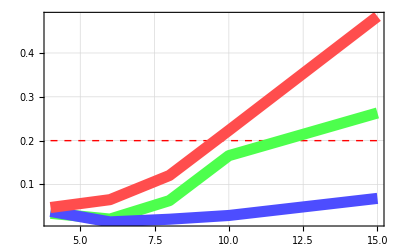

```mathematica
(*
Now graph averages... 
*)
pavgTLaccum=avgTLaccum//ListPlot[#,PlotStyle->{Lighter[Green,.3], Thickness[.02]},Joined->True,PlotTheme->"Detailed",PlotRange->All,ImageSize->400]&;
pavgTAaccum=avgTAaccum//ListPlot[#,PlotStyle->{Lighter[Blue,.3],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotRange->All,ImageSize->400]&;
pavgNTaccum=avgNTaccum//ListPlot[#,PlotStyle->{Lighter[Red,.3],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotRange->All,ImageSize->400]&;
line = ListPlot[{{4,.2},{15,.2}},PlotStyle->{Red,Thickness[0.0025], Dashed},Joined->True,PlotTheme->"Detailed",PlotRange->All,ImageSize->400];
Show[line,pavgTLaccum,pavgTAaccum,pavgNTaccum, PlotRange->All]
```

```mathematica
(*
Now calculate error at each time point. 
The error is the deviation of the averages...  
*)
```

```mathematica
a = Transpose[myNT2[[All,4,1,2;;6,2]]]
```

{{0.1,0.,0.,,,0.05,0.,0.,0.,0.,0.1,0.,0.},{0.1,0.,0.,,,0.05,0.,0.,0.,0.,0.,0.,0.},{0.,0.7,0.,,,0.05,0.,0.,0.,0.1,0.,0.,0.},{0.,1.,0.,,,0.05,0.2,0.,0.,0.5,0.,0.,0.},{,1.,0.,,,0.05,0.8,0.,,0.8,0.,0.4,}}

```mathematica
Table[a[[i]]//Cases[#,x_/; x ≠ ""]& ,{i,1,5,1}]
```

{{0.1,0.,0.,0.05,0.,0.,0.,0.,0.1,0.,0.},{0.1,0.,0.,0.05,0.,0.,0.,0.,0.,0.,0.},{0.,0.7,0.,0.05,0.,0.,0.,0.1,0.,0.,0.},{0.,1.,0.,0.05,0.2,0.,0.,0.5,0.,0.,0.},{1.,0.,0.05,0.8,0.,0.8,0.,0.4}}

```mathematica
(*
Remove all the zeros out of NT accumulation data {{data at time 1},{data at time 2}, {...}}
*)
accumNT1trans = Transpose[myNT1[[All,4,1,2;;6,2]]];rmNT1 =Table[accumNT1trans[[i]]//Cases[#,x_/; x≠ ""]&,{i,1,5,1}]
Length/@rmNT1
accumNT2trans = Transpose[myNT2[[All,4,1,2;;6,2]]];rmNT2 =Table[accumNT2trans[[i]]//Cases[#,x_/; x≠ ""]&,{i,1,5,1}]
Length/@rmNT2
accumNT3trans = Transpose[myNT3[[All,2,1,2;;6,2]]];rmNT3 =Table[accumNT3trans[[i]]//Cases[#,x_/; x≠ ""]&,{i,1,5,1}]
Length/@rmNT3
```

{{0.,0.2,0.,0.2,0.15,0.2,0.,0.2,0.,0.2,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.3,0.,0.3,0.2,0.1,0.,0.,0.,0.7,0.,0.,0.5,0.,0.,0.,0.,0.},{0.,0.2,0.,0.3,0.,0.,0.,0.6,0.2,0.85,0.,0.,0.8,0.1,0.,0.5,0.4,0.},{1.,0.2,0.15,0.3,-0.2,0.,0.,0.95,0.,0.95,0.,0.,0.9,0.5,0.,0.7,0.7,0.},{1.,0.4,0.2,0.8,-0.1,0.4,0.3,0.95,0.95,0.95,0.,0.9,0.9,0.2,0.8,0.85,0.}}

{18,18,18,18,17}

{{0.1,0.,0.,0.05,0.,0.,0.,0.,0.1,0.,0.},{0.1,0.,0.,0.05,0.,0.,0.,0.,0.,0.,0.},{0.,0.7,0.,0.05,0.,0.,0.,0.1,0.,0.,0.},{0.,1.,0.,0.05,0.2,0.,0.,0.5,0.,0.,0.},{1.,0.,0.05,0.8,0.,0.8,0.,0.4}}

{11,11,11,11,8}

{{0.,0.1,0.05,0.15,0.1,0.2,0.,0.,0.1,0.,0.05,0.,0.,0.},{0.,0.,0.,0.1,0.1,0.1,0.,0.,0.,0.,0.1,0.,0.,0.},{0.,0.,0.,0.1,0.1,0.05,0.,0.,0.,0.,0.25,0.,0.,0.},{0.,0.,0.1,0.3,0.2,0.15,0.,0.,0.,0.1,0.5,0.,0.4,0.01},{0.,0.5,0.25,0.9,0.3,0.75,0.6,0.5,0.1,0.,0.8,0.1,0.7,0.8}}

{14,14,14,14,14}

```mathematica
(*
Remove all the zeros out of TA accumulation data {{data at time 1},{data at time 2}, {...}}
*)
accumTA1trans = Transpose[myTA1[[All,4,1,2;;6,2]]];rmTA1 =Table[accumTA1trans[[i]]//Cases[#,x_/; x≠ ""]&,{i,1,5,1}]
Length/@rmTA1
accumTA2trans = Transpose[myTA2[[All,4,1,2;;6,2]]];rmTA2 =Table[accumTA2trans[[i]]//Cases[#,x_/; x≠ ""]&,{i,1,5,1}]
Length/@rmTA2
accumTA3trans = Transpose[myTA3[[All,2,1,2;;6,2]]];rmTA3 =Table[accumTA3trans[[i]]//Cases[#,x_/; x≠ ""]&,{i,1,5,1}]
Length/@rmTA3
```

{{0.,0.1,0.,0.1,0.,0.,0.,0.1,0.,0.1,0.1},{0.,0.1,0.,0.,0.,0.,0.1,0.,0.,0.1},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

{11,10,10,10,10}

{{0.,0.,-0.05,0.05,0.,0.,0.03,0.1,0.2,0.1,0.3,0.05,0.08,0.15,0.,0.05},{0.,0.,0.,0.,0.,0.,0.,0.1,0.05,0.75,0.,0.05,0.05,0.,0.05},{0.,0.,0.,0.,0.,0.,0.,0.1,0.,0.75,0.,0.,0.6,0.15},{0.,0.,0.,0.,0.,0.,0.,0.15,0.,0.75,0.,0.1,0.8,0.15},{0.05,0.,0.1,0.,0.6,0.,0.,0.25,0.5,0.,0.8,0.8}}

{16,15,14,14,12}

{{0.05,0.,0.05,0.,0.,0.,0.,0.1,0.1,0.,0.15,0.1,0.,0.,0.05,0.,0.,0.1,0.05,0.1},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.05,0.,0.05},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

{20,20,20,20,20}

```mathematica
(*
Remove all the zeros out of TL accumulation data {{data at time 1},{data at time 2}, {...}}
*)
accumTL2trans = Transpose[myTL2[[All,4,1,2;;6,2]]];rmTL2 =Table[accumTL2trans[[i]]//Cases[#,x_/; NumericQ[x]]&,{i,1,5,1}]
Length/@rmTL2
accumTL3trans = Transpose[myTL3[[All,2,1,2;;6,2]]];rmTL3 =Table[accumTL3trans[[i]]//Cases[#,x_/; x≠ ""]&,{i,1,5,1}]
Length/@rmTL3
```

{{0.,0.,0.,0.,0.,0.,0.,0.05,0.,0.05,0.,0.05},{0.,0.,0.1,0.,0.,0.,0.,0.15,0.,0.,0.},{0.25,0.8,0.,0.,0.,0.,0.,0.},{0.7,0.9,0.,0.,0.,0.,0.,0.3},{0.85,0.9,0.,0.,0.,0.4}}

{12,11,8,8,6}

{{0.,0.,0.,0.,0.1,0.1,0.1,0.15,0.,0.,0.,0.1,0.},{0.,0.,0.,0.,0.,0.1,0.,0.05,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.15,0.,0.,0.},{0.,0.4,0.,0.35,0.,0.,0.1,0.,0.05,0.3,0.05,0.,0.},{0.,0.75,0.,0.6,0.,0.,0.3,0.1,0.3,0.35,0.3,0.,0.15}}

{13,13,13,13,13}

```mathematica
(*
Now that you have these 3 data sets, calc averages of each... 
*)
```

```mathematica
Transpose[{Mean/@rmNT1,Mean/@rmNT2,Mean/@rmNT3}]
Transpose[{Mean/@rmTA1,Mean/@rmTA2,Mean/@rmTA3}]
Transpose[{Mean/@rmTL2,Mean/@rmTL3}]
```

{{0.0638889,0.0227273,0.0535714},{0.116667,0.0136364,0.0285714},{0.219444,0.0772727,0.0357143},{0.341667,0.159091,0.125714},{0.558824,0.38125,0.45}}

{{0.0454545,0.06625,0.0425},{0.03,0.07,0.005},{0.,0.114286,0.},{0.,0.139286,0.005},{0.,0.258333,0.01}}

{{0.0125,0.0423077},{0.0227273,0.0115385},{0.13125,0.0115385},{0.2375,0.0961538},{0.358333,0.219231}}

### BELOW: dev

```mathematica
tempList = Transpose[rmNT1[[All, 1,2;;All,2]]];
```

```mathematica
tempList[[1,2]]
```

0.2

```mathematica
Table[Cases[rmNT3[[All,i]],x_/;NumericQ[x⟦2⟧]],{i,2,6,1}]
```

Part::partw: Part 2 of {{{accum,Cy3 accum},{4.,0.},{6.,0.},{8.,0.},{10.,0.},{15.,0.}}} does not exist.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

Part::partd: Part specification 2⟦2⟧ is longer than depth of object.

Part::partw: Part 3 of {{{accum,Cy3 accum},{4.,0.},{6.,0.},{8.,0.},{10.,0.},{15.,0.}}} does not exist.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 4 of {{{accum,Cy3 accum},{4.,0.},{6.,0.},{8.,0.},{10.,0.},{15.,0.}}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{},{},{},{},{}}

```mathematica
tempAvt = Cases[Table[Mean[Cases[rmNT3[[All,i]],x_/;NumericQ[x[[2]]]]],{i,2,6,1}],x_/;Length[x]==2]
```

Part::partw: Part 2 of {{{accum,Cy3 accum},{4.,0.},{6.,0.},{8.,0.},{10.,0.},{15.,0.}}} does not exist.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

Part::partd: Part specification 2⟦2⟧ is longer than depth of object.

Part::partw: Part 3 of {{{accum,Cy3 accum},{4.,0.},{6.,0.},{8.,0.},{10.,0.},{15.,0.}}} does not exist.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 4 of {{{accum,Cy3 accum},{4.,0.},{6.,0.},{8.,0.},{10.,0.},{15.,0.}}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{}

```mathematica
Cases[tempList, x_/;Table[Table[x[[i,j]]/= "",{j,1,Length@tempList[[1]],1}],{i,1,Length@tempList,1}]]
```

Part::partd: Part specification {0.,0.2,0.,0.2,0.15,0.2,0.,0.2,0.,0.2,0.,0.,0.,0.,0.,0.,0.,0.}⟦1,1⟧ is longer than depth of object.

Set::setps: {0.,0.2,0.,0.2,0.15,0.2,0.,0.2,0.,0.2,0.,0.,0.,0.,0.,0.,0.,0.} in the part assignment is not a symbol.

Part::partd: Part specification {0.,0.2,0.,0.2,0.15,0.2,0.,0.2,0.,0.2,0.,0.,0.,0.,0.,0.,0.,0.}⟦1,2⟧ is longer than depth of object.

Set::setps: {0.,0.2,0.,0.2,0.15,0.2,0.,0.2,0.,0.2,0.,0.,0.,0.,0.,0.,0.,0.} in the part assignment is not a symbol.

Part::partd: Part specification {0.,0.2,0.,0.2,0.15,0.2,0.,0.2,0.,0.2,0.,0.,0.,0.,0.,0.,0.,0.}⟦1,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Set::setps: {0.,0.2,0.,0.2,0.15,0.2,0.,0.2,0.,0.2,0.,0.,0.,0.,0.,0.,0.,0.} in the part assignment is not a symbol.

General::stop: Further output of Set::setps will be suppressed during this calculation.

{}

```mathematica
Cases[#,x_/;x⟦6,2⟧>.2]&
```

```mathematica
μNT1 = Mean/@rmNT1[[2;;All]]
```

{{{hours,Cy3 Accum (%)},{4.,0.2},{6.,0.3},{8.,0.2},{10.,0.2},{15.,0.4},{20.,0.4}},{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,0.},{10.,0.15},{15.,0.2},{20.,0.2}},{{hours,Cy3 Accum (%)},{4.,0.2},{6.,0.3},{8.,0.3},{10.,0.3},{15.,0.8},{20.,0.95}},{{hours,Cy3 Accum (%)},{4.,0.15},{6.,0.2},{8.,0.},{10.,-0.2},{15.,-0.1},{20.,0.3}},{{hours,Cy3 Accum (%)},{4.,0.2},{6.,0.1},{8.,0.},{10.,0.},{15.,0.4},{20.,0.4}},{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,0.},{10.,0.},{15.,0.3},{20.,0.4}},{{hours,Cy3 Accum (%)},{4.,0.2},{6.,0.},{8.,0.6},{10.,0.95},{15.,},{20.,}},{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,0.2},{10.,0.},{15.,0.95},{20.,0.95}},{{hours,Cy3 Accum (%)},{4.,0.2},{6.,0.7},{8.,0.85},{10.,0.95},{15.,0.95},{20.,1.}},{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,0.},{10.,0.},{15.,0.95},{20.,1.}},{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,0.},{10.,0.},{15.,0.},{20.,0.}},{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.5},{8.,0.8},{10.,0.9},{15.,0.9},{20.,0.9}},{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,0.1},{10.,0.5},{15.,0.9},{20.,0.9}},{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,0.},{10.,0.},{15.,0.2},{20.,0.3}},{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,0.5},{10.,0.7},{15.,0.8},{20.,0.8}},{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,0.4},{10.,0.7},{15.,0.85},{20.,0.9}},{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,0.},{10.,0.},{15.,0.},{20.,0.}}}

```mathematica
Needs["ErrorBarPlots`"];
{μavgTLaccum,σNT}
```

{μavgTLaccum,σNT}